# Metadata Landscapes

## Rijksmuseum Semantic Explorer — Notebook 5 of 5

The Rijksmuseum's vocabulary database associates each artwork with structured metadata: object types, materials, techniques, and subjects drawn from a controlled vocabulary of nearly 150,000 terms. This notebook explores how these categorical labels relate to each other and to the embedding space. Co-occurrence matrices reveal which materials go with which types; centroid comparisons measure semantic similarity between categories; separability analysis tests whether the embedding model has learned to distinguish object types; and word clouds show the thematic focus of each category. Together, these analyses map the metadata landscape of the collection.

## 1. Data Loading

```mathematica
dataDir = FileNameJoin[{NotebookDirectory[], "data"}];
If[!DirectoryQ[dataDir],
  Print["Data not found. Run: uv run python export_for_mathematica.py"];
  Abort[]];
manifest = Import[FileNameJoin[{dataDir, "metadata.json"}], "RawJSON"];
{n, dim} = Lookup[manifest, {"n", "dim"}];
raw = BinaryReadList[FileNameJoin[{dataDir, "embeddings.bin"}], "Real32"];
embeddings = Partition[raw, dim];
artIds = manifest["art_ids"];
artworks = manifest["artworks"];
Print["Loaded ", n, " embeddings"]
```

Loaded 20000 embeddings

## 2. Metadata Extraction

```mathematica
(* Extract all metadata fields *)
allTypes = Table[artworks[ToString[id]]["types"], {id, artIds}];
allCreators = Table[artworks[ToString[id]]["creators"], {id, artIds}];
allSubjects = Table[artworks[ToString[id]]["subjects"], {id, artIds}];
allMaterials = Table[artworks[ToString[id]]["materials"], {id, artIds}];
allTechniques = Table[artworks[ToString[id]]["techniques"], {id, artIds}];

Print["Unique types: ", Length[Union[Flatten[allTypes]]]]
Print["Unique materials: ", Length[Union[Flatten[allMaterials]]]]
Print["Unique techniques: ", Length[Union[Flatten[allTechniques]]]]
Print["Unique subjects: ", Length[Union[Flatten[allSubjects]]]]
```

Unique types: 1048

Unique materials: 310

Unique techniques: 430

Unique subjects: 13887

## 3. Category Frequencies

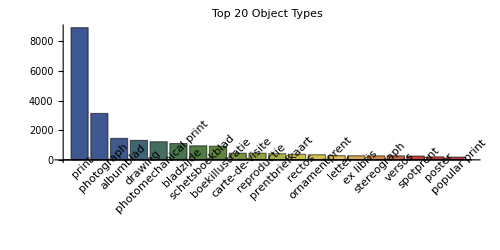
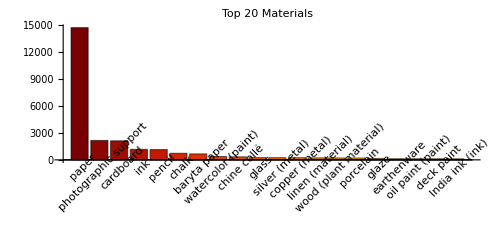
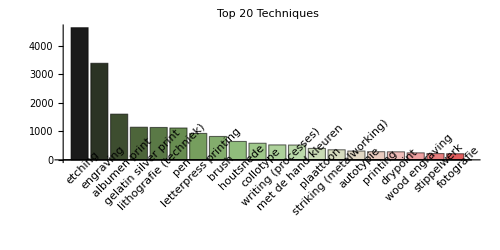
-Graphics- | -Graphics-
-Graphics- |

```mathematica
typeCounts = TakeLargest[Counts[Flatten[allTypes]], 20];
materialCounts = TakeLargest[Counts[Flatten[allMaterials]], 20];
techniqueCounts = TakeLargest[Counts[Flatten[allTechniques]], 20];

Grid[{
  {BarChart[Values[typeCounts],
    ChartLabels -> Placed[Keys[typeCounts], Below, Rotate[#, Pi/4, {-1, 0}] &],
    PlotLabel -> "Top 20 Object Types", ChartStyle -> "DarkRainbow",
    ImageSize -> 500, AspectRatio -> 1/2],
   BarChart[Values[materialCounts],
    ChartLabels -> Placed[Keys[materialCounts], Below, Rotate[#, Pi/4, {-1, 0}] &],
    PlotLabel -> "Top 20 Materials", ChartStyle -> "SolarColors",
    ImageSize -> 500, AspectRatio -> 1/2]},
  {BarChart[Values[techniqueCounts],
    ChartLabels -> Placed[Keys[techniqueCounts], Below, Rotate[#, Pi/4, {-1, 0}] &],
    PlotLabel -> "Top 20 Techniques", ChartStyle -> "WatermelonColors",
    ImageSize -> 500, AspectRatio -> 1/2],
   SpanFromLeft}
}]
```

## 4. Type × Material Co-occurrence

Different types of art objects call for different materials: paintings use oil paint and canvas, prints use paper and ink, photographs use photographic paper. The co-occurrence matrix quantifies these associations by counting how often each type-material pair appears together across the collection. The log scale is necessary because counts span several orders of magnitude — a few dominant combinations (e.g., print + paper) vastly outnumber rare pairings. Bright cells in the heatmap mark strong associations, while dark cells indicate combinations that rarely or never occur, revealing the material constraints of each artistic tradition.

```mathematica
topTypeNames = Keys[TakeLargest[Counts[Flatten[allTypes]], 12]];
topMatNames = Keys[TakeLargest[Counts[Flatten[allMaterials]], 12]];

(* Build co-occurrence matrix efficiently *)
coocCounts = Association[];
Do[
  Module[{types = allTypes[[i]], mats = allMaterials[[i]]},
    Do[
      Module[{key = {t, m}},
        coocCounts[key] = Lookup[coocCounts, Key[key], 0] + 1],
      {t, Intersection[types, topTypeNames]},
      {m, Intersection[mats, topMatNames]}]],
  {i, n}];

coocMatrix = Table[
  Lookup[coocCounts, Key[{t, m}], 0],
  {t, topTypeNames}, {m, topMatNames}];

MatrixPlot[Log[coocMatrix + 1],
  FrameTicks -> {
    {Thread[{Range[Length[topTypeNames]], topTypeNames}], None},
    {Thread[{Range[Length[topMatNames]], topMatNames}], None}},
  PlotLabel -> "Type × Material Co-occurrence (log scale)",
  ColorFunction -> "Viridis",
  PlotLegends -> BarLegend[{"Viridis", {0, Max[Log[coocMatrix + 1]]}},
    LegendLabel -> "log(count+1)"],
  ImageSize -> 650]
```

MatrixPlot::cfun: The value of the option ColorFunction -> Viridis is not a valid color function or a gradient ColorData entity.

-Graphics-

## 5. Category Centroids in Embedding Space

Just as we computed creator centroids earlier, we can compute a centroid embedding for each metadata category — the average embedding of all artworks labelled with that attribute. Similarity between these centroids reveals whether the embedding model sees certain categories as semantically related. For instance, 'painting' and 'drawing' might have similar centroids (both are two-dimensional depictions), while 'furniture' and 'photograph' might be distant. The resulting similarity matrix for the top 15 object types provides a semantic taxonomy that may differ from the museum's formal classification hierarchy.

```mathematica
(* Type centroids *)
topTypes = Keys[TakeLargest[Counts[Flatten[allTypes]], 15]];
typeCentroids = Association[Table[
  Module[{mask = Flatten[Position[allTypes, _?(MemberQ[#, t] &)]]},
    If[Length[mask] > 0,
      t -> <|"centroid" -> Normalize[Mean[embeddings[[mask]]]],
             "count" -> Length[mask]|>,
      Nothing]],
  {t, topTypes}]];

(* Type similarity matrix *)
typeNames = Keys[typeCentroids];
typeCentMat = typeCentroids[#]["centroid"] & /@ typeNames;
typeSimMat = Outer[Dot, typeCentMat, typeCentMat, 1];

MatrixPlot[typeSimMat,
  FrameTicks -> {
    {Thread[{Range[Length[typeNames]], typeNames}], None},
    {Thread[{Range[Length[typeNames]], typeNames}], None}},
  PlotLabel -> "Object Type Semantic Similarity",
  ColorFunction -> "TemperatureMap",
  PlotLegends -> Automatic,
  ImageSize -> 550]
```

-Graphics-

## 6. Category Separability

Separability measures whether different object types occupy distinct, non-overlapping regions of embedding space or whether they blend together. For each type, we compute two quantities: the mean intra-type distance (how spread out the type's artworks are around their centroid) and the mean inter-type distance (how far the centroid is from other types' centroids). The ratio of inter to intra distance is the separability score: values above 1 mean the type forms a distinct cluster with clear boundaries, while values near or below 1 mean the type overlaps substantially with others. The red dashed line at ratio=1 marks this boundary. Types with high separability are those the embedding model can most reliably distinguish.

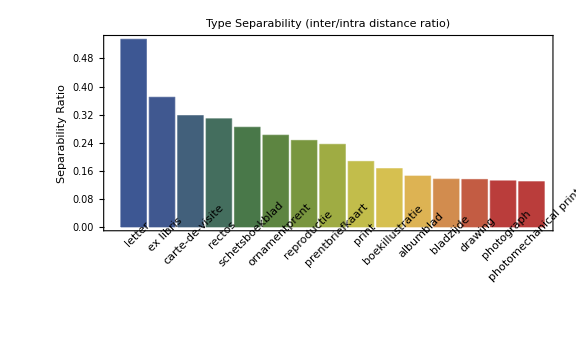

```mathematica
separability = Association[Table[
  Module[{mask, typeEmbs, centroid, meanIntraDist, interDists},
    mask = Flatten[Position[allTypes, _?(MemberQ[#, t] &)]];
    typeEmbs = embeddings[[mask]];
    centroid = typeCentroids[t]["centroid"];
    meanIntraDist = Mean[1 - typeEmbs.centroid];
    interDists = Table[
      1 - centroid.typeCentroids[t2]["centroid"],
      {t2, Select[typeNames, # != t &]}];
    t -> <|"intra" -> meanIntraDist,
            "inter" -> Mean[interDists],
            "ratio" -> Mean[interDists] / Max[meanIntraDist, 0.001],
            "count" -> Length[mask]|>],
  {t, typeNames}]];

sepData = Reverse[SortBy[Normal[separability], #[[2]]["ratio"] &]];
BarChart[#[[2]]["ratio"] & /@ sepData,
  ChartLabels -> Placed[#[[1]] & /@ sepData, Below, Rotate[#, Pi/4, {-1, 0}] &],
  PlotLabel -> "Type Separability (inter/intra distance ratio)",
  AxesLabel -> {None, "Separability Ratio"},
  ChartStyle -> "DarkRainbow",
  PlotTheme -> "Scientific",
  GridLines -> {None, {1}},
  GridLinesStyle -> {Red, Dashed},
  ImageSize -> Large]
```

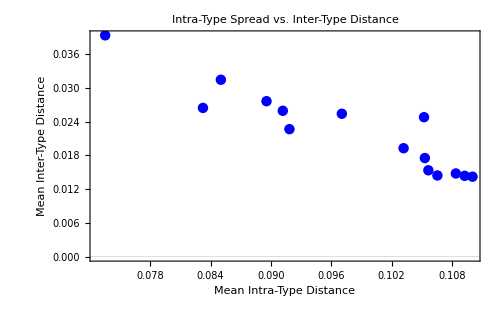

```mathematica
(* Intra vs Inter distance scatter *)
ListPlot[
  Table[
    Tooltip[{separability[t]["intra"], separability[t]["inter"]}, t],
    {t, typeNames}],
  PlotLabel -> "Intra-Type Spread vs. Inter-Type Distance",
  AxesLabel -> {"Mean Intra-Type Distance", "Mean Inter-Type Distance"},
  PlotStyle -> Directive[PointSize[0.015], Blue],
  PlotTheme -> "Scientific",
  Epilog -> {Red, Dashed, InfiniteLine[{0, 0}, {1, 1}]},
  ImageSize -> 500,
  PlotRange -> All]
```

## 7. Subject Analysis by Object Type

Each object type in the collection tends to depict characteristic subjects. Paintings might emphasise portraits and landscapes, prints might focus on maps and allegories, photographs on architecture and events. Word clouds visualise the subject distribution for each of the top object types, with word size proportional to frequency. Comparing these clouds across types reveals both the expected thematic specialisations and surprising overlaps — subjects that appear prominently in multiple object types represent themes the museum documents across media.

print (8933 works)

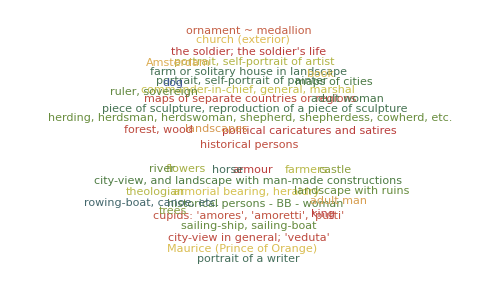

photograph (3137 works)

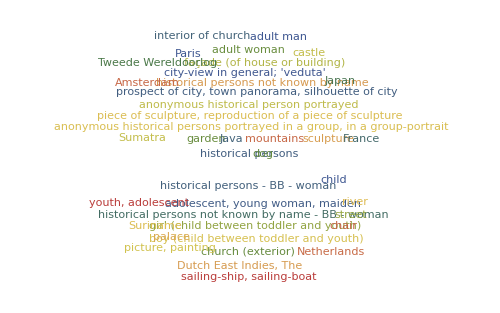

albumblad (1451 works)

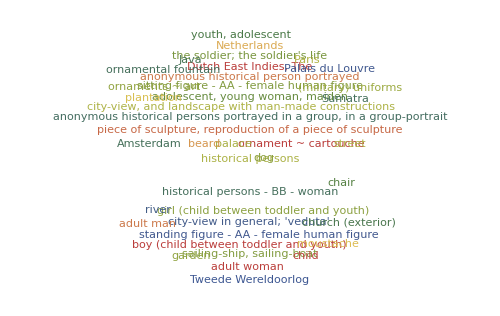

drawing (1317 works)

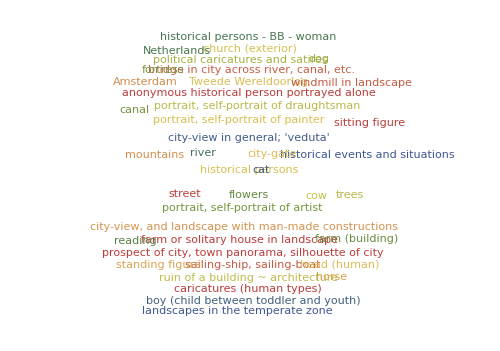

photomechanical print (1224 works)

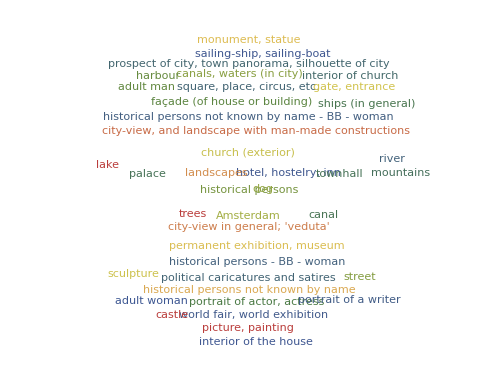

bladzijde (1104 works)

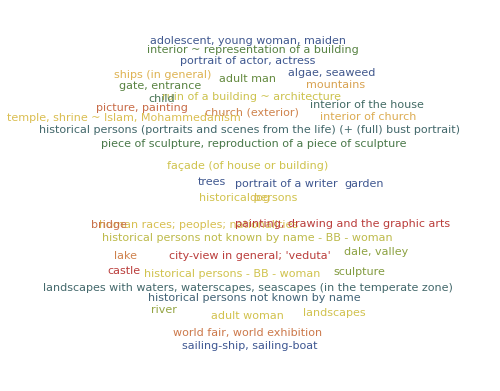

```mathematica
showTypes = Keys[typeCentroids][[1 ;; Min[6, Length[typeCentroids]]]];
Do[
  Module[{mask, subjects, counts},
    mask = Flatten[Position[allTypes, _?(MemberQ[#, t] &)]];
    subjects = Flatten[allSubjects[[mask]]];
    If[Length[subjects] > 0,
      counts = TakeLargest[Counts[subjects], Min[40, Length[Union[subjects]]]];
      Print[Style[t <> " (" <> ToString[Length[mask]] <> " works)", 14, Bold]];
      Print[WordCloud[counts, ImageSize -> 500,
        ColorFunction -> (ColorData["DarkRainbow"][RandomReal[]] &)]];
      Print[""]
    ]],
  {t, showTypes}]
```

## 8. Object Type Similarity Network

The type similarity network represents each object type as a vertex, with edges connecting types whose centroid cosine similarity exceeds a threshold (0.8). Edge thickness encodes similarity strength, vertex size encodes the number of artworks of that type (on a log scale), and vertex colour encodes the separability score computed earlier. This graph gives an intuitive, spatial view of the type landscape: tightly connected clusters of types share semantic content, while isolated vertices represent categories with unique embedding signatures. The spring-embedding layout naturally places similar types close together.

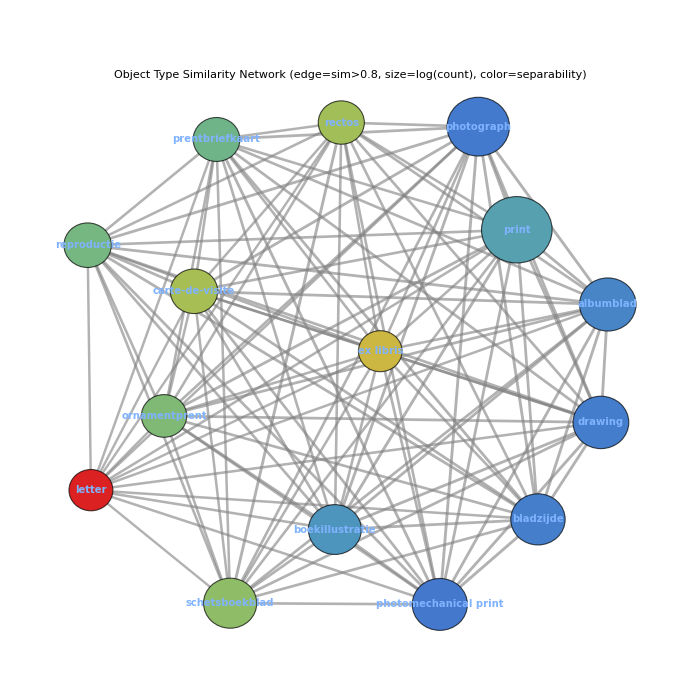

```mathematica
(* Build type similarity graph *)
typeEdges = Flatten[Table[
  If[i < j && typeSimMat[[i, j]] > 0.8,
    {UndirectedEdge[typeNames[[i]], typeNames[[j]]]},
    {}],
  {i, Length[typeNames]}, {j, Length[typeNames]}]];

typeWeights = Table[
  typeSimMat[[
    First[Flatten[Position[typeNames, e[[1]]]]],
    First[Flatten[Position[typeNames, e[[2]]]]]]],
  {e, typeEdges}];

Graph[typeNames, typeEdges,
  EdgeWeight -> typeWeights,
  EdgeStyle -> Table[typeEdges[[i]] ->
    Directive[Thickness[0.003 * typeWeights[[i]]^4], Opacity[0.6], Gray],
    {i, Length[typeEdges]}],
  VertexLabels -> Placed["Name", Center],
  VertexSize -> Table[v -> Log[2, typeCentroids[v]["count"]] / 20, {v, typeNames}],
  VertexStyle -> Table[v ->
    ColorData["Rainbow"][separability[v]["ratio"] / Max[#[[2]]["ratio"] & /@ sepData]],
    {v, typeNames}],
  VertexLabelStyle -> Directive[10, Bold],
  GraphLayout -> "SpringEmbedding",
  PlotLabel -> "Object Type Similarity Network\n(edge=sim>0.8, size=log(count), color=separability)",
  ImageSize -> 700]
```

## 9. Material-Technique Relationships

Materials and techniques are closely coupled in art production: etching requires a metal plate, watercolour requires paper, weaving requires thread. The material-technique co-occurrence matrix reveals these craft traditions quantitatively, showing which technique-material pairings dominate the collection. The companion material similarity matrix computes cosine similarity between material centroids in embedding space, revealing which materials produce semantically similar artworks regardless of technique. Together, these two views distinguish physical constraints (which materials technically require which techniques) from semantic affinities (which materials yield similar artwork content).

```mathematica
topTechNames = Keys[TakeLargest[Counts[Flatten[allTechniques]], 10]];
matTechNames = Keys[TakeLargest[Counts[Flatten[allMaterials]], 10]];

(* Material-technique co-occurrence *)
matTechCooc = Association[];
Do[
  Module[{mats = allMaterials[[i]], techs = allTechniques[[i]]},
    Do[
      Module[{key = {m, t}},
        matTechCooc[key] = Lookup[matTechCooc, Key[key], 0] + 1],
      {m, Intersection[mats, matTechNames]},
      {t, Intersection[techs, topTechNames]}]],
  {i, n}];

matTechMatrix = Table[
  Lookup[matTechCooc, Key[{m, t}], 0],
  {m, matTechNames}, {t, topTechNames}];

MatrixPlot[Log[matTechMatrix + 1],
  FrameTicks -> {
    {Thread[{Range[Length[matTechNames]], matTechNames}], None},
    {Thread[{Range[Length[topTechNames]], topTechNames}], None}},
  PlotLabel -> "Material × Technique Co-occurrence (log scale)",
  ColorFunction -> "SunsetColors",
  PlotLegends -> BarLegend[{"SunsetColors", {0, Max[Log[matTechMatrix + 1]]}},
    LegendLabel -> "log(count+1)"],
  ImageSize -> 600]
```

-Graphics-

```mathematica
(* Material centroids - which materials produce similar embeddings? *)
matCentroids = Association[Table[
  Module[{mask = Flatten[Position[allMaterials, _?(MemberQ[#, m] &)]]},
    If[Length[mask] >= 20,
      m -> Normalize[Mean[embeddings[[mask]]]],
      Nothing]],
  {m, matTechNames}]];

matNames = Keys[matCentroids];
matCentMat = Values[matCentroids];
matSimMat = matCentMat.Transpose[matCentMat];

MatrixPlot[matSimMat,
  FrameTicks -> {
    {Thread[{Range[Length[matNames]], matNames}], None},
    {Thread[{Range[Length[matNames]], matNames}], None}},
  PlotLabel -> "Material Semantic Similarity",
  ColorFunction -> "TemperatureMap",
  PlotLegends -> Automatic,
  ImageSize -> 500]
```

-Graphics-